```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WLEDA.xlsx"]
```

```mathematica
data1={{-90.,0.},{-80.,0.},{-70.,0.},{-60.,0.},{-50.,10.73},{-40.,22.03},{-30.,38.97},{-20.,111.8},{-10.,3287.1},{0.,20628.},{10.,2313.7},{20.,114.1},{30.,39.54},{40.,23.16},{50.,10.73},{60.,0.},{70.,0.},{80.,0.},{90.,0.}};
```

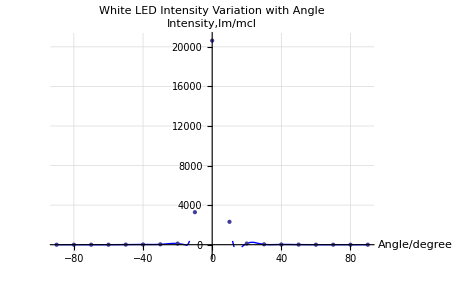

```mathematica
Show[gra1=ListLinePlot[data1,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Intensity,lm/mcl"},PlotLabel->"White LED Intensity Variation with Angle",GridLines->Automatic],ListPlot[data1],PlotRange->{-1000,21000}]
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BLEDA.xlsx"]
```

```mathematica
data2={{-90.,0.},{-80.,0.},{-70.,0.},{-60.,0.},{-50.,0.},{-40.,0.},{-30.,0.},{-20.,0.},{-15.,97.72},{-10.,269.4},{-5.,391.4},{0.,460.9},{5.,382.4},{10.,236.1},{15.,107.8},{20.,5.648},{30.,0.},{40.,0.},{50.,0.},{60.,0.},{70.,0.},{80.,0.},{90.,0.}};
```

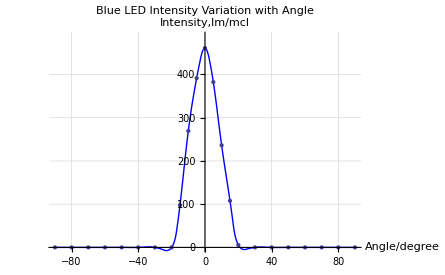

```mathematica
Show[gra2=ListLinePlot[data2,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Intensity,lm/mcl"},PlotLabel->"Blue LED Intensity Variation with Angle",GridLines->Automatic],ListPlot[data2],PlotRange->{0,488}]
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GLEDA.xlsx"]
```

```mathematica
data3={{-90.,0.},{-80.,0.},{-70.,0.},{-60.,0.},{-50.,0.},{-40.,5.608},{-35.,6.213},{-30.,8.473},{-20.,15.81},{-10.,1075.5},{0.,2086.6},{10.,1259.1},{20.,130.4},{30.,6.213},{40.,0.},{50.,0.},{60.,0.},{70.,0.},{80.,0.},{90.,0.}};
```

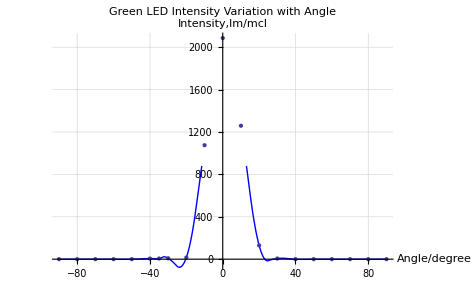

```mathematica
Show[gra3=ListLinePlot[data3,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Intensity,lm/mcl"},PlotLabel->"Green LED Intensity Variation with Angle",GridLines->Automatic],ListPlot[data3],PlotRange->{-50,2090}]
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WA.xlsx"]
```

```mathematica
data4={{-90.,0.},{-80.,7.928},{-70.,35.02},{-60.,67.68},{-50.,69.48},{-40.,80.77},{-30.,96.03},{-20.,150.2},{-10.,3071.8},{0.,3403.4},{10.,2602.4},{20.,133.8},{30.,109.},{40.,90.38},{50.,69.48},{60.,62.83},{70.,24.29},{80.,5.648},{90.,0.}};
```

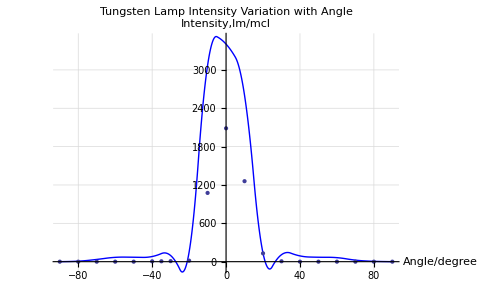

```mathematica
Show[gra4=ListLinePlot[data4,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Intensity,lm/mcl"},PlotLabel->"Tungsten Lamp Intensity Variation with Angle",GridLines->Automatic],ListPlot[data3],PlotRange->{-100,3500}]
```